```mathematica
ClearAll["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]
```

```mathematica
Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

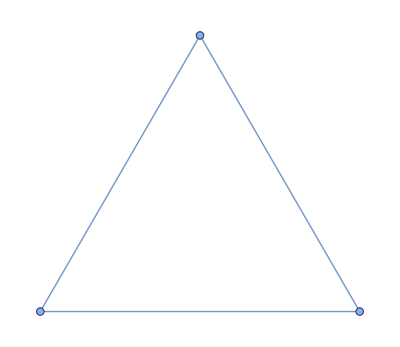

{2,-1,-1}

{{2/(-1+λ)}}

```mathematica
K = AdjacencyGraph[{{0,1,1},{1,0,1},{1,1,0}}]
Eigenvalues[MyAdjacencyMatrix[K]]
Simplify[Smash[K,{1}]]
```

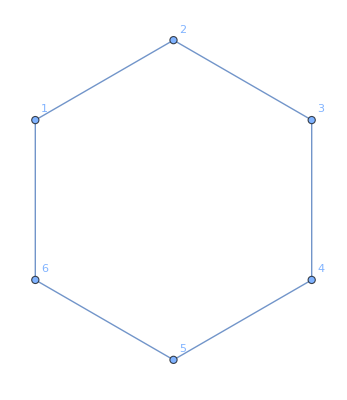

{{0,1,0,0,0,1},{1,0,1,0,0,0},{0,1,0,1,0,0},{0,0,1,0,1,0},{0,0,0,1,0,1},{1,0,0,0,1,0}}

{-2,2,-1,-1,1,1}

{{(2 (-2+λ^2))/(λ (-3+λ^2))}}

(-4+5 λ^2-λ^4)/(-3 λ+λ^3)

{{λ→-2},{λ→-1},{λ→1},{λ→2}}

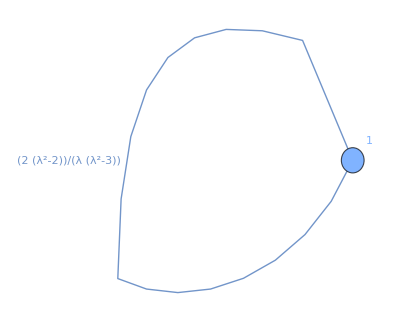

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,5<->6,6<->1}, VertexLabels->"Name"]
MyAdjacencyMatrix[G]
Eigenvalues[MyAdjacencyMatrix[G]]
adjmat = Simplify[Smash[G,{1}]]
Det[adjmat - λ IdentityMatrix[1]]
Solve[Det[adjmat - λ IdentityMatrix[1]]==0,{λ}]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1}]
```

-Graphics-

{{(2 (-2+λ^2))/(λ (-3+λ^2))}}

-Graphics-

{{(λ (-2+λ^2))/(1-3 λ^2+λ^4),1+1/(1-3 λ^2+λ^4)},{1+1/(1-3 λ^2+λ^4),(λ (-2+λ^2))/(1-3 λ^2+λ^4)}}

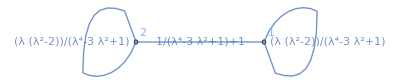

{{(3-2 λ^2)/(2 λ-λ^3),(-1+λ^2)/(λ (-2+λ^2))},{(-1+λ^2)/(λ (-2+λ^2)),(3-2 λ^2)/(2 λ-λ^3)}}

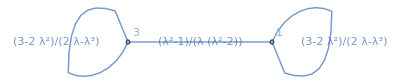

{{(2 λ)/(-1+λ^2),2/(-1+λ^2)},{2/(-1+λ^2),(2 λ)/(-1+λ^2)}}

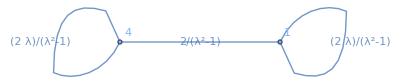

{{(3-2 λ^2)/(2 λ-λ^3),(-1+λ^2)/(λ (-2+λ^2))},{(-1+λ^2)/(λ (-2+λ^2)),(3-2 λ^2)/(2 λ-λ^3)}}

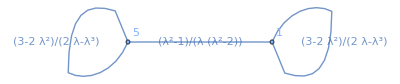

{{(λ (-2+λ^2))/(1-3 λ^2+λ^4),1+1/(1-3 λ^2+λ^4)},{1+1/(1-3 λ^2+λ^4),(λ (-2+λ^2))/(1-3 λ^2+λ^4)}}

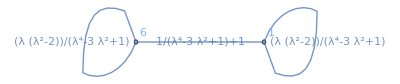

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,5<->6,6<->1}, VertexLabels->"Name"]
adjmat = Simplify[Smash[G,{1}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1}]
adjmat = Simplify[Smash[G,{1,2}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->2}]
adjmat = Simplify[Smash[G,{1,3}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->3}]
adjmat = Simplify[Smash[G,{1,4}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->4}]
adjmat = Simplify[Smash[G,{1,5}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->5}]
adjmat = Simplify[Smash[G,{1,6}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->6}]
```

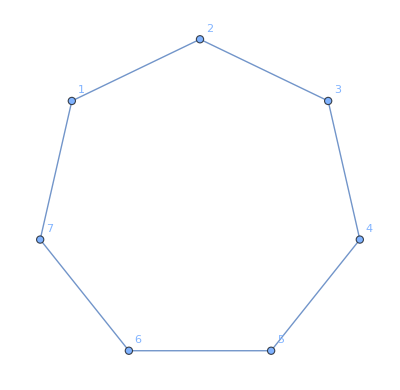

{{(2 (-1-λ+λ^2))/(1-2 λ-λ^2+λ^3)}}

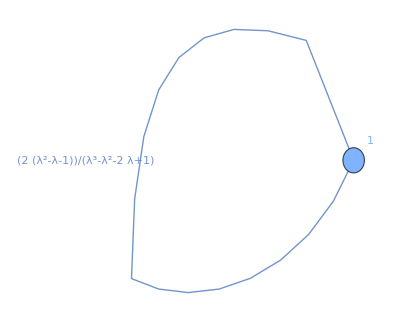

{{(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5),1+1/(3 λ-4 λ^3+λ^5)},{1+1/(3 λ-4 λ^3+λ^5),(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5)}}

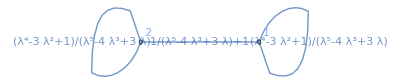

{{(1-5 λ^2+2 λ^4)/(λ-3 λ^3+λ^5),(1+λ-3 λ^2+λ^4)/(λ-3 λ^3+λ^5)},{(1+λ-3 λ^2+λ^4)/(λ-3 λ^3+λ^5),(1-5 λ^2+2 λ^4)/(λ-3 λ^3+λ^5)}}

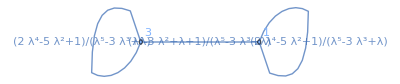

{{(1-4 λ^2+2 λ^4)/(2 λ-3 λ^3+λ^5),(-1-2 λ+λ^2+λ^3)/(λ (2-3 λ^2+λ^4))},{(-1-2 λ+λ^2+λ^3)/(λ (2-3 λ^2+λ^4)),(1-4 λ^2+2 λ^4)/(2 λ-3 λ^3+λ^5)}}

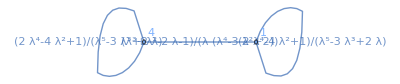

{{(1-4 λ^2+2 λ^4)/(2 λ-3 λ^3+λ^5),(-1-2 λ+λ^2+λ^3)/(λ (2-3 λ^2+λ^4))},{(-1-2 λ+λ^2+λ^3)/(λ (2-3 λ^2+λ^4)),(1-4 λ^2+2 λ^4)/(2 λ-3 λ^3+λ^5)}}

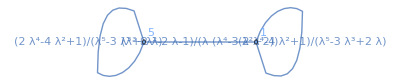

{{(1-5 λ^2+2 λ^4)/(λ-3 λ^3+λ^5),(1+λ-3 λ^2+λ^4)/(λ-3 λ^3+λ^5)},{(1+λ-3 λ^2+λ^4)/(λ-3 λ^3+λ^5),(1-5 λ^2+2 λ^4)/(λ-3 λ^3+λ^5)}}

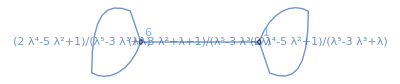

{{(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5),1+1/(3 λ-4 λ^3+λ^5)},{1+1/(3 λ-4 λ^3+λ^5),(1-3 λ^2+λ^4)/(3 λ-4 λ^3+λ^5)}}

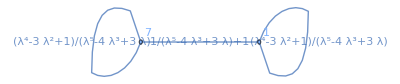

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,5<->6,6<->7,7<->1}, VertexLabels->"Name"]
adjmat = Simplify[Smash[G,{1}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1}]
adjmat = Simplify[Smash[G,{1,2}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->2}]
adjmat = Simplify[Smash[G,{1,3}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->3}]
adjmat = Simplify[Smash[G,{1,4}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->4}]
adjmat = Simplify[Smash[G,{1,5}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->5}]
adjmat = Simplify[Smash[G,{1,6}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->6}]
adjmat = Simplify[Smash[G,{1,7}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->7}]
```

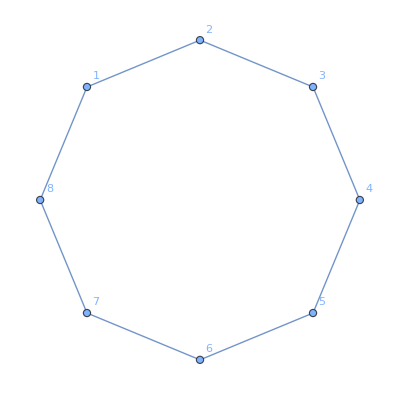

{{(2 λ (-3+λ^2))/(2-4 λ^2+λ^4)}}

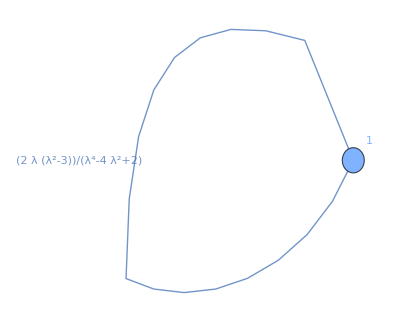

{{(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6),1+1/(-1+6 λ^2-5 λ^4+λ^6)},{1+1/(-1+6 λ^2-5 λ^4+λ^6),(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6)}}

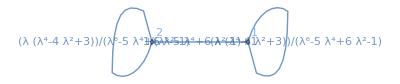

{{(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5),((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4))},{((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4)),(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5)}}

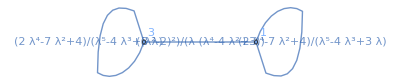

{{(λ (3-6 λ^2+2 λ^4))/(-1+4 λ^2-4 λ^4+λ^6),(λ^2 (-2+λ^2))/(-1+4 λ^2-4 λ^4+λ^6)},{(λ^2 (-2+λ^2))/(-1+4 λ^2-4 λ^4+λ^6),(λ (3-6 λ^2+2 λ^4))/(-1+4 λ^2-4 λ^4+λ^6)}}

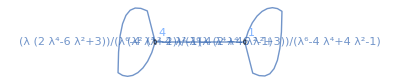

{{(2 (-1+λ^2))/(λ (-2+λ^2)),2/(-2 λ+λ^3)},{2/(-2 λ+λ^3),(2 (-1+λ^2))/(λ (-2+λ^2))}}

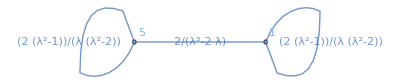

{{(λ (3-6 λ^2+2 λ^4))/(-1+4 λ^2-4 λ^4+λ^6),(λ^2 (-2+λ^2))/(-1+4 λ^2-4 λ^4+λ^6)},{(λ^2 (-2+λ^2))/(-1+4 λ^2-4 λ^4+λ^6),(λ (3-6 λ^2+2 λ^4))/(-1+4 λ^2-4 λ^4+λ^6)}}

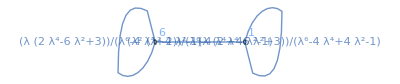

{{(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5),((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4))},{((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4)),(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5)}}

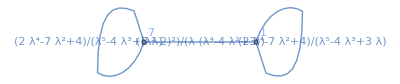

{{(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5),((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4))},{((-2+λ^2)^2)/(λ (3-4 λ^2+λ^4)),(4-7 λ^2+2 λ^4)/(3 λ-4 λ^3+λ^5)}}

-Graphics-

{{(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6),1+1/(-1+6 λ^2-5 λ^4+λ^6)},{1+1/(-1+6 λ^2-5 λ^4+λ^6),(λ (3-4 λ^2+λ^4))/(-1+6 λ^2-5 λ^4+λ^6)}}

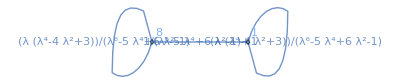

```mathematica
G = Graph[{1<->2, 2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->1}, VertexLabels->"Name"]
adjmat = Simplify[Smash[G,{1}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1}]
adjmat = Simplify[Smash[G,{1,2}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->2}]
adjmat = Simplify[Smash[G,{1,3}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->3}]
adjmat = Simplify[Smash[G,{1,4}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->4}]
adjmat = Simplify[Smash[G,{1,5}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->5}]
adjmat = Simplify[Smash[G,{1,6}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->6}]
adjmat = Simplify[Smash[G,{1,7}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->7}]
adjmat = Simplify[Smash[G,{1,7}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->7}]
adjmat = Simplify[Smash[G,{1,8}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1,2->8}]
```

```mathematica
graphs=GraphData/@GraphData["Connected",7];
```

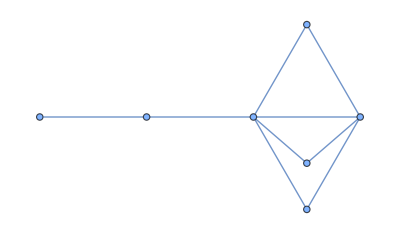

{{(2 (-3-5 λ+λ^3))/(λ (-6-7 λ+λ^3))}}

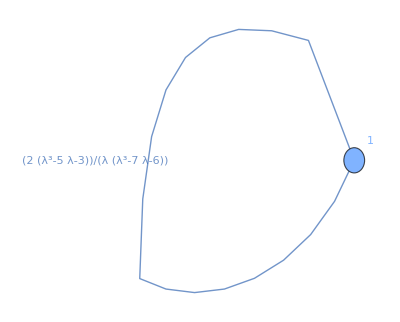

```mathematica
G=graphs[[8]]
adjmat = Simplify[Smash[G,{1}]]
g=WeightedAdjacencyGraph[adjmat];
Graph[g,EdgeLabels->"EdgeWeight",VertexLabels->{1->1}]
```

```mathematica
graphs=GraphData/@GraphData["Connected",3];
```

```mathematica
results=Table[
Module[{adjmat,reduced},
adjmat=Simplify[Smash[graphs[[i]],{1}]];
reduced=WeightedAdjacencyGraph[adjmat];
<|
"Index"->i,
"Graph"->graphs[[i]],
"ReducedMatrix"->adjmat,
"ReducedGraph"->reduced
|>
],
{i,Length[graphs]}
];
```

```mathematica
Table[Eigenvalues[results[[i,"ReducedMatrix"]]],{i,Length[results]}]
```

{{λ/(-1+λ^2)},{2/(-1+λ)}}

```mathematica
Tally[Flatten[MatrixEntries/@(results[[All,"ReducedMatrix"]])]]
```

{{MatrixEntries[{{λ/(-1+λ^2)}}],1},{MatrixEntries[{{2/(-1+λ)}}],1}}